# Flow Test Files

```mathematica
<<NounouW`
```

<<KazukazuM version 0.5.20110118 loaded on: Tue 25 Jan 2011 19:25:24>>

<<NounouM version 0.5.20110119 loaded on: Tue 25 Jan 2011 19:25:25>>

```mathematica
dataScale=0.305175781250000;
```

## Test File Import (for header)--do once at beginning

```mathematica
cd=SetDirectory[NotebookDirectory[]]
```

V:\Documents\k.vsd\_figures\vsdMeth\flow field

```mathematica
data=BinaryReadList["test_spiral.da","Integer16"];
```

```mathematica
Length[data]
```

98848

```mathematica
header=Take[data, 2560];
data=Drop[data,2560];
```

```mathematica
Dimensions /@{header, data}
```

{{2560},{96288}}

```mathematica
header[[{5,97}]]
```

{202,472}

```mathematica
96288-202*472
```

944

```mathematica
footer=Take[data,-944];
```

```mathematica
data=Drop[data,-944];
data=Partition[data,202];
Dimensions[data]
```

{472,202}

```mathematica
ListLinePlot[data[[ Range[1,464, 70 ]  ]] ]//Rasterize
```

-Graphics-

## Confirmation with NNM--do once at beginning

```mathematica
dataobj=NNMDataNew[cd<>"//test_spiral.da"];
```

```mathematica
ListLinePlot[dataobj@readDataTraceAbsolute[#]& /@ Range[0,463, 70 ] ]//Rasterize
```

-Graphics-

## Layout Related--do once at beginning

```mathematica
LoadJavaClass[$NNMDataLayoutDefaultClassPath]
```

JavaClass[edu.georgetown.nnj.data.layout.NNJDataLayout464ii,<>]

```mathematica
layout=NNJDataLayout464ii`INSTANCE
```

«JavaObject[edu.georgetown.nnj.data.layout.NNJDataLayout464ii]»

```mathematica
field={(layout@getDetectorField[])@getX[],(layout@getDetectorField[])@getY[],
(layout@getDetectorField[])@getWidth[],(layout@getDetectorField[])@getHeight[]}
```

{0.,0.,1.×10^7,8.66025×10^6}

```mathematica
radius=layout@getDetectorRadius[]
```

200000

```mathematica
centerDetector=layout@getDetectorCoordinates[123-1]
```

{5100000,4356922}

```mathematica
Options[NNMDetectorCircles]
```

{PlotChannels→All,DetectorShape→Circle,Filling→False,PageFlipFactor→{1,1},PlotStyle→Directive[Opacity[0.5,GrayLevel[0]]],ReturnPrimitives→False,GraphicsOptions→{}}

```mathematica
oneSin[x_]:=Sin[x]*UnitBox[(x/Pi-0.5)]
```

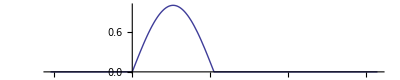

```mathematica
Plot[oneSin[x],{x,-Pi, 3 Pi},AspectRatio->1/5]
```

```mathematica
repeatedOneSin[x_]:=oneSin[Mod[x,3*2Pi]];
```

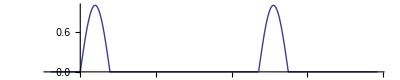

```mathematica
Plot[repeatedOneSin[x],{x,-Pi, 10Pi},AspectRatio->1/5,PlotRange->All]
```

## Serialize

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Kenta\Documents\k.vsd\_documents\_figures\vsdMeth\flow field

```mathematica
(*Save["flowTestData.m",{header,data,footer,field, radius, centerDetector}]*)
```

```mathematica
Get["flowTestData.m"]
```

{5100000,4356922}

```mathematica
LoadJavaClass[$NNMDataLayoutDefaultClassPath]
```

JavaClass[edu.georgetown.nnj.data.layout.NNJDataLayout464ii,<>]

```mathematica
layout=NNJDataLayout464ii`INSTANCE
```

«JavaObject[edu.georgetown.nnj.data.layout.NNJDataLayout464ii]»

## Translation

```mathematica
translationFunction[detDiameterPer2Pi_,framesPerDetDiameter_, angle_, noisePercent_]:=
( oneSin[  (1/(2*radius){ #1-centerDetector[[1]],#2-centerDetector[[2]]}.{Cos[angle/360*2 Pi],Sin[angle/360*2 Pi]}-#3/framesPerDetDiameter)/detDiameterPer2Pi *2*Pi]
+noisePercent/100*Random[Real,{-1,1}])&;
```

### Testing

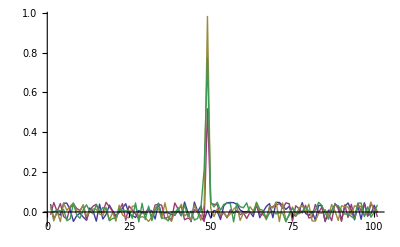

```mathematica
ListLinePlot[
Table[
Table[ translationFunction[detDiameterPer2Pi,0.1,60, 5][0,0,fr], {fr,-50,50}],
{detDiameterPer2Pi, {5,10,20,30}}], PlotRange->All]
```

```mathematica
gr=Show[
DensityPlot[
translationFunction[20,1,60,10][x,y,-5],{x,0,1*10^7},{y,0,8.7*10^6},
Mesh->False,ColorFunction->NNMColorMap,PlotRange->All,PlotPoints->100,MaxRecursion->0],
Graphics[Translate[Scale[NNMDetectorCircles[PlotStyle->Directive[Black, AbsoluteThickness[10]],ReturnPrimitives->True],10000],centerDetector]],AspectRatio->Automatic
]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["translation.jpg",gr,ImageSize->5000]
```

translation.jpg

```mathematica
Show[
DensityPlot[
translationFunction[20,1,60,10][x,y,-5],{x,0,1*10^7},{y,0,8.66025*10^6},
Mesh->False,ColorFunction->NNMColorMap,PlotPoints->200 ],
Graphics[Translate[Scale[NNMDetectorCircles[PlotStyle->Directive[Black, Thick],ReturnPrimitives->True],10000],centerDetector]],AspectRatio->Automatic
]//Rasterize
```

```mathematica
Show[GraphicsArray[
Table[DensityPlot[
translationFunction[10,10,60,10][x,y,fr],{x,0,1*10^7},{y,0,8.66025*10^6},
PlotPoints->100, Mesh->False,AspectRatio->Automatic,Frame->None] ,{fr,0,100,20}]
],ImageSize->72*10]//Rasterize
```

-Graphics-

## Translation-- Da File Generation

The minimum speed 5 frames per detector diameter would need approximately 12*5=60 frames to exit (or enter) the field. Therefore, I will give -200 to 200 for the frames, and analyze between frame 100-300 (of 400 total frames) in the test

```mathematica
translationDa[detDiameterPer2Pi_,framesPerDetDiameter_, angle_, noisePercent_]:=
Module[{tempdata},
tempdata=
Module[{coordinates},
Table[
coordinates=layout@getDetectorCoordinates[det];
Table[  translationFunction[detDiameterPer2Pi,framesPerDetDiameter,angle,noisePercent][coordinates[[1]],coordinates[[2]],frame],
{frame, -200,200}],
{det,0,471}]
];
SetDirectory[NotebookDirectory[]];
header[[5]]=Length[tempdata[[1]]];
data=BinaryWrite[ ".\\testfiles\\translation_"<>ToString[detDiameterPer2Pi]<>"_"<>ToString[framesPerDetDiameter]<>"_"<>ToString[angle]<>"_"<>ToString[noisePercent]<>".da",
Flatten[{header,Round[tempdata*1000/dataScale],footer}],
"Integer16"]
]
```

```mathematica
translationDa[30,#, 60,0]& /@ Join[Range[0.1, 1, 0.1],Range[1.25,5.0,0.25]]
```

{.\testfiles\translation_30_0.1_60_0.da,.\testfiles\translation_30_0.2_60_0.da,.\testfiles\translation_30_0.3_60_0.da,.\testfiles\translation_30_0.4_60_0.da,.\testfiles\translation_30_0.5_60_0.da,.\testfiles\translation_30_0.6_60_0.da,.\testfiles\translation_30_0.7_60_0.da,.\testfiles\translation_30_0.8_60_0.da,.\testfiles\translation_30_0.9_60_0.da,.\testfiles\translation_30_1._60_0.da,.\testfiles\translation_30_1.25_60_0.da,.\testfiles\translation_30_1.5_60_0.da,.\testfiles\translation_30_1.75_60_0.da,.\testfiles\translation_30_2._60_0.da,.\testfiles\translation_30_2.25_60_0.da,.\testfiles\translation_30_2.5_60_0.da,.\testfiles\translation_30_2.75_60_0.da,.\testfiles\translation_30_3._60_0.da,.\testfiles\translation_30_3.25_60_0.da,.\testfiles\translation_30_3.5_60_0.da,.\testfiles\translation_30_3.75_60_0.da,.\testfiles\translation_30_4._60_0.da,.\testfiles\translation_30_4.25_60_0.da,.\testfiles\translation_30_4.5_60_0.da,.\testfiles\translation_30_4.75_60_0.da,.\testfiles\translation_30_5._60_0.da}

```mathematica
translationDa[30,#, 60,0]& /@ Range[5.0, 10.0, 1.0]
```

{.\testfiles\translation_30_5._60_0.da,.\testfiles\translation_30_6._60_0.da,.\testfiles\translation_30_7._60_0.da,.\testfiles\translation_30_8._60_0.da,.\testfiles\translation_30_9._60_0.da,.\testfiles\translation_30_10._60_0.da}

```mathematica
translationDa[20,#, 60,5]& /@ Join[Range[0.1, 1, 0.1],Range[1.25,5.0,0.25]]
```

$Aborted

```mathematica
translationDa[20,#, 60,10]& /@ Join[Range[0.1, 1, 0.1],Range[1.25,5.0,0.25]]
```

{.\testfiles\translation_10_0.1_60_10.da,.\testfiles\translation_10_0.2_60_10.da,.\testfiles\translation_10_0.3_60_10.da,.\testfiles\translation_10_0.4_60_10.da,.\testfiles\translation_10_0.5_60_10.da,.\testfiles\translation_10_0.6_60_10.da,.\testfiles\translation_10_0.7_60_10.da,.\testfiles\translation_10_0.8_60_10.da,.\testfiles\translation_10_0.9_60_10.da,.\testfiles\translation_10_1._60_10.da,.\testfiles\translation_10_1.25_60_10.da,.\testfiles\translation_10_1.5_60_10.da,.\testfiles\translation_10_1.75_60_10.da,.\testfiles\translation_10_2._60_10.da,.\testfiles\translation_10_2.25_60_10.da,.\testfiles\translation_10_2.5_60_10.da,.\testfiles\translation_10_2.75_60_10.da,.\testfiles\translation_10_3._60_10.da,.\testfiles\translation_10_3.25_60_10.da,.\testfiles\translation_10_3.5_60_10.da,.\testfiles\translation_10_3.75_60_10.da,.\testfiles\translation_10_4._60_10.da,.\testfiles\translation_10_4.25_60_10.da,.\testfiles\translation_10_4.5_60_10.da,.\testfiles\translation_10_4.75_60_10.da,.\testfiles\translation_10_5._60_10.da}

```mathematica
translationDa[20,#, 60,15]& /@ Join[Range[0.1, 1, 0.1],Range[1.25,5.0,0.25]]
```

{.\testfiles\translation_10_0.1_60_15.da,.\testfiles\translation_10_0.2_60_15.da,.\testfiles\translation_10_0.3_60_15.da,.\testfiles\translation_10_0.4_60_15.da,.\testfiles\translation_10_0.5_60_15.da,.\testfiles\translation_10_0.6_60_15.da,.\testfiles\translation_10_0.7_60_15.da,.\testfiles\translation_10_0.8_60_15.da,.\testfiles\translation_10_0.9_60_15.da,.\testfiles\translation_10_1._60_15.da,.\testfiles\translation_10_1.25_60_15.da,.\testfiles\translation_10_1.5_60_15.da,.\testfiles\translation_10_1.75_60_15.da,.\testfiles\translation_10_2._60_15.da,.\testfiles\translation_10_2.25_60_15.da,.\testfiles\translation_10_2.5_60_15.da,.\testfiles\translation_10_2.75_60_15.da,.\testfiles\translation_10_3._60_15.da,.\testfiles\translation_10_3.25_60_15.da,.\testfiles\translation_10_3.5_60_15.da,.\testfiles\translation_10_3.75_60_15.da,.\testfiles\translation_10_4._60_15.da,.\testfiles\translation_10_4.25_60_15.da,.\testfiles\translation_10_4.5_60_15.da,.\testfiles\translation_10_4.75_60_15.da,.\testfiles\translation_10_5._60_15.da}

```mathematica
translationDa[10,#, 60,20]& /@ Join[Range[0.1, 1, 0.1],Range[1.25,5.0,0.25]]
```

{.\testfiles\translation_10_0.1_60_20.da,.\testfiles\translation_10_0.2_60_20.da,.\testfiles\translation_10_0.3_60_20.da,.\testfiles\translation_10_0.4_60_20.da,.\testfiles\translation_10_0.5_60_20.da,.\testfiles\translation_10_0.6_60_20.da,.\testfiles\translation_10_0.7_60_20.da,.\testfiles\translation_10_0.8_60_20.da,.\testfiles\translation_10_0.9_60_20.da,.\testfiles\translation_10_1._60_20.da,.\testfiles\translation_10_1.25_60_20.da,.\testfiles\translation_10_1.5_60_20.da,.\testfiles\translation_10_1.75_60_20.da,.\testfiles\translation_10_2._60_20.da,.\testfiles\translation_10_2.25_60_20.da,.\testfiles\translation_10_2.5_60_20.da,.\testfiles\translation_10_2.75_60_20.da,.\testfiles\translation_10_3._60_20.da,.\testfiles\translation_10_3.25_60_20.da,.\testfiles\translation_10_3.5_60_20.da,.\testfiles\translation_10_3.75_60_20.da,.\testfiles\translation_10_4._60_20.da,.\testfiles\translation_10_4.25_60_20.da,.\testfiles\translation_10_4.5_60_20.da,.\testfiles\translation_10_4.75_60_20.da,.\testfiles\translation_10_5._60_20.da}

```mathematica
translationDa[10,#, 60,25]& /@ Join[Range[0.1, 1, 0.1],Range[1.25,5.0,0.25]]
```

{.\testfiles\translation_10_0.1_60_25.da,.\testfiles\translation_10_0.2_60_25.da,.\testfiles\translation_10_0.3_60_25.da,.\testfiles\translation_10_0.4_60_25.da,.\testfiles\translation_10_0.5_60_25.da,.\testfiles\translation_10_0.6_60_25.da,.\testfiles\translation_10_0.7_60_25.da,.\testfiles\translation_10_0.8_60_25.da,.\testfiles\translation_10_0.9_60_25.da,.\testfiles\translation_10_1._60_25.da,.\testfiles\translation_10_1.25_60_25.da,.\testfiles\translation_10_1.5_60_25.da,.\testfiles\translation_10_1.75_60_25.da,.\testfiles\translation_10_2._60_25.da,.\testfiles\translation_10_2.25_60_25.da,.\testfiles\translation_10_2.5_60_25.da,.\testfiles\translation_10_2.75_60_25.da,.\testfiles\translation_10_3._60_25.da,.\testfiles\translation_10_3.25_60_25.da,.\testfiles\translation_10_3.5_60_25.da,.\testfiles\translation_10_3.75_60_25.da,.\testfiles\translation_10_4._60_25.da,.\testfiles\translation_10_4.25_60_25.da,.\testfiles\translation_10_4.5_60_25.da,.\testfiles\translation_10_4.75_60_25.da,.\testfiles\translation_10_5._60_25.da}

```mathematica
translationDa[10,#, 60,30]& /@ Join[Range[0.1, 1, 0.1],Range[1.25,5.0,0.25]]
```

{.\testfiles\translation_10_0.1_60_30.da,.\testfiles\translation_10_0.2_60_30.da,.\testfiles\translation_10_0.3_60_30.da,.\testfiles\translation_10_0.4_60_30.da,.\testfiles\translation_10_0.5_60_30.da,.\testfiles\translation_10_0.6_60_30.da,.\testfiles\translation_10_0.7_60_30.da,.\testfiles\translation_10_0.8_60_30.da,.\testfiles\translation_10_0.9_60_30.da,.\testfiles\translation_10_1._60_30.da,.\testfiles\translation_10_1.25_60_30.da,.\testfiles\translation_10_1.5_60_30.da,.\testfiles\translation_10_1.75_60_30.da,.\testfiles\translation_10_2._60_30.da,.\testfiles\translation_10_2.25_60_30.da,.\testfiles\translation_10_2.5_60_30.da,.\testfiles\translation_10_2.75_60_30.da,.\testfiles\translation_10_3._60_30.da,.\testfiles\translation_10_3.25_60_30.da,.\testfiles\translation_10_3.5_60_30.da,.\testfiles\translation_10_3.75_60_30.da,.\testfiles\translation_10_4._60_30.da,.\testfiles\translation_10_4.25_60_30.da,.\testfiles\translation_10_4.5_60_30.da,.\testfiles\translation_10_4.75_60_30.da,.\testfiles\translation_10_5._60_30.da}

```mathematica
translationDa[10,3, #,0]& /@ Range[0,90, 3]
```

{.\testfiles\translation_10_3_0_0.da,.\testfiles\translation_10_3_3_0.da,.\testfiles\translation_10_3_6_0.da,.\testfiles\translation_10_3_9_0.da,.\testfiles\translation_10_3_12_0.da,.\testfiles\translation_10_3_15_0.da,.\testfiles\translation_10_3_18_0.da,.\testfiles\translation_10_3_21_0.da,.\testfiles\translation_10_3_24_0.da,.\testfiles\translation_10_3_27_0.da,.\testfiles\translation_10_3_30_0.da,.\testfiles\translation_10_3_33_0.da,.\testfiles\translation_10_3_36_0.da,.\testfiles\translation_10_3_39_0.da,.\testfiles\translation_10_3_42_0.da,.\testfiles\translation_10_3_45_0.da,.\testfiles\translation_10_3_48_0.da,.\testfiles\translation_10_3_51_0.da,.\testfiles\translation_10_3_54_0.da,.\testfiles\translation_10_3_57_0.da,.\testfiles\translation_10_3_60_0.da,.\testfiles\translation_10_3_63_0.da,.\testfiles\translation_10_3_66_0.da,.\testfiles\translation_10_3_69_0.da,.\testfiles\translation_10_3_72_0.da,.\testfiles\translation_10_3_75_0.da,.\testfiles\translation_10_3_78_0.da,.\testfiles\translation_10_3_81_0.da,.\testfiles\translation_10_3_84_0.da,.\testfiles\translation_10_3_87_0.da,.\testfiles\translation_10_3_90_0.da}

```mathematica
translationDa[10,3, 60,#]& /@ Range[0,50, 2]
```

{.\testfiles\translation_10_3_60_0.da,.\testfiles\translation_10_3_60_2.da,.\testfiles\translation_10_3_60_4.da,.\testfiles\translation_10_3_60_6.da,.\testfiles\translation_10_3_60_8.da,.\testfiles\translation_10_3_60_10.da,.\testfiles\translation_10_3_60_12.da,.\testfiles\translation_10_3_60_14.da,.\testfiles\translation_10_3_60_16.da,.\testfiles\translation_10_3_60_18.da,.\testfiles\translation_10_3_60_20.da,.\testfiles\translation_10_3_60_22.da,.\testfiles\translation_10_3_60_24.da,.\testfiles\translation_10_3_60_26.da,.\testfiles\translation_10_3_60_28.da,.\testfiles\translation_10_3_60_30.da,.\testfiles\translation_10_3_60_32.da,.\testfiles\translation_10_3_60_34.da,.\testfiles\translation_10_3_60_36.da,.\testfiles\translation_10_3_60_38.da,.\testfiles\translation_10_3_60_40.da,.\testfiles\translation_10_3_60_42.da,.\testfiles\translation_10_3_60_44.da,.\testfiles\translation_10_3_60_46.da,.\testfiles\translation_10_3_60_48.da,.\testfiles\translation_10_3_60_50.da}

### Testing

```mathematica
tempdata=
Module[{coordinates},
Table[
coordinates=layout@getDetectorCoordinates[det];
Table[  translationFunction[10,5,60,10][coordinates[[1]],coordinates[[2]],frame],
{frame, 0,400}],
{det,0,471}]
];
```

```mathematica
NNMFramePlot[First[Transpose[tempdata]]]//Rasterize
```

-Graphics-

```mathematica
cd=SetDirectory[NotebookDirectory[]]
```

Z:\My Documents\k.vsd\_documents\_figures\vsdMeth\flow field

```mathematica
$ByteOrdering
```

-1

```mathematica
header[[5]]=Length[tempdata[[1]]]; header[[5]]
```

401

```mathematica
data=BinaryWrite[ "translation_10_5_60_10.da",
Flatten[{header,Round[tempdata*1000/dataScale],footer}],
"Integer16"]
```

translation_10_5_60_10.da

### Test

```mathematica
dataobj=NNMDataNew[cd<>".//testfiles//translation_30_0.5_60_0.da"];
```

```mathematica
ListLinePlot[dataobj@readDataTraceAbsolute[#]& /@ Range[0,463, 70 ],PlotRange->{{150,250},All} ]//Rasterize
```

-Graphics-

```mathematica
dataobj=NNMDataNew[cd<>".//testfiles//translation_30_0.1_60_0.da"];
```

```mathematica
ListLinePlot[dataobj@readDataTraceAbsolute[#]& /@ RandomInteger[{0,463}, 50 ],PlotRange->{{190,210},All} ]//Rasterize
```

-Graphics-

```mathematica
ListLinePlot[
Arg[K`hilbert[#].{1,ⅈ}]&  /@(dataobj@readDataTraceAbsolute[#]& /@ Range[0,463, 70 ])
] //Rasterize
```

-Graphics-

## Source

```mathematica
sourceFunction[detDiameterPer2Pi_,framesPerDetDiameter_, noisePercent_]:=
sourceFunction[detDiameterPer2Pi,framesPerDetDiameter, noisePercent]=
(oneSin[
(Norm[{#1-centerDetector[[1]],#2-centerDetector[[2]]}]/(2*radius)-#3/framesPerDetDiameter)
/detDiameterPer2Pi*2Pi]
+noisePercent/100*Random[Real,{-1,1}])&;
```

```mathematica
radius
```

200000

### Testing

```mathematica
Graphics[Translate[Scale[NNMDetectorCircles[PlotStyle->Directive[Black, AbsoluteThickness[10]],ReturnPrimitives->True],10000],centerDetector]],AspectRatio->Automatic
```

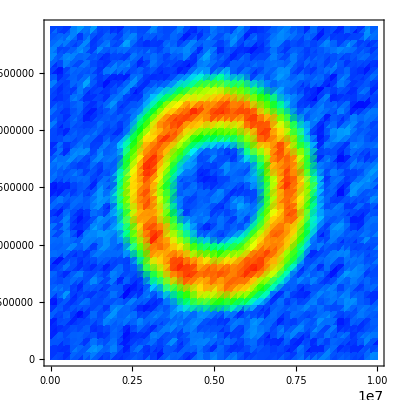

```mathematica
gr=DensityPlot[
sourceFunction[10,5,10][x,y,15],{x,0,1*10^7},{y,0,8.7*10^6},
Mesh->False,ColorFunction->NNMColorMap,PlotRange->All,PlotPoints->(*100*)50,MaxRecursion->0]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["source.jpg",gr,ImageSize->5000]
```

source.jpg

```mathematica
Remove[sourceFunction]
```

```mathematica
Show[GraphicsArray[
Table[DensityPlot[
sourceFunction[10,10,25][x,y,fr],{x,0,1*10^7},{y,0,8.66025*10^6},
PlotPoints->100, Mesh->False,AspectRatio->Automatic,Frame->None] ,{fr,0,100,10}]
],ImageSize->72*14]//Rasterize
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

```mathematica
layout@getDetectorCoordinates[1]
```

{7100000,8513844}

## Source-- Da File Generation

```mathematica
sourceDa[detDiameterPer2Pi_,framesPerDetDiameter_, noisePercent_]:=
Module[{tempdata},
tempdata=
Module[{coordinates},
Table[
coordinates=layout@getDetectorCoordinates[det];
Table[  sourceFunction[detDiameterPer2Pi,framesPerDetDiameter,noisePercent][coordinates[[1]],coordinates[[2]],frame],
{frame, -300,300}],
{det,0,471}]
];
SetDirectory[NotebookDirectory[]];
header[[5]]=Length[tempdata[[1]]];
data=BinaryWrite[ ".\\testfiles\\source_"<>ToString[detDiameterPer2Pi]<>"_"<>ToString[framesPerDetDiameter]<>"_"<>ToString[noisePercent]<>".da",
Flatten[{header,Round[tempdata*1000/dataScale],footer}],
"Integer16"]
]
```

```mathematica
sourceDa[10,#, 0]& /@ Range[6.0,10.0,0.5]
```

{.\testfiles\source_10_6._0.da,.\testfiles\source_10_6.5_0.da,.\testfiles\source_10_7._0.da,.\testfiles\source_10_7.5_0.da,.\testfiles\source_10_8._0.da,.\testfiles\source_10_8.5_0.da,.\testfiles\source_10_9._0.da,.\testfiles\source_10_9.5_0.da,.\testfiles\source_10_10._0.da}

```mathematica
sourceDa[10,#, 0]& /@ Join[Range[0.05, 0.45, 0.05],Range[0.5,5.5,0.5]]
```

{.\testfiles\source_10_0.05_0.da,.\testfiles\source_10_0.1_0.da,.\testfiles\source_10_0.15_0.da,.\testfiles\source_10_0.2_0.da,.\testfiles\source_10_0.25_0.da,.\testfiles\source_10_0.3_0.da,.\testfiles\source_10_0.35_0.da,.\testfiles\source_10_0.4_0.da,.\testfiles\source_10_0.45_0.da,.\testfiles\source_10_0.5_0.da,.\testfiles\source_10_1._0.da,.\testfiles\source_10_1.5_0.da,.\testfiles\source_10_2._0.da,.\testfiles\source_10_2.5_0.da,.\testfiles\source_10_3._0.da,.\testfiles\source_10_3.5_0.da,.\testfiles\source_10_4._0.da,.\testfiles\source_10_4.5_0.da,.\testfiles\source_10_5._0.da,.\testfiles\source_10_5.5_0.da}

### Testing

```mathematica
tempdata=
Module[{coordinates},
Table[
coordinates=layout@getDetectorCoordinates[det];
Table[  sourceFunction[5,5,10][coordinates[[1]],coordinates[[2]],frame],
{frame, 0,400}],
{det,0,471}]
];
```

```mathematica
NNMFramePlot[First[Transpose[tempdata]]]//Rasterize
```

-Graphics-

```mathematica
cd=SetDirectory[NotebookDirectory[]]
```

Z:\My Documents\k.vsd\_documents\_figures\vsdMeth\flow field

```mathematica
$ByteOrdering
```

-1

```mathematica
header[[5]]=Length[tempdata[[1]]]; header[[5]]
```

401

```mathematica
data=BinaryWrite[ "source_10_5_10.da",
Flatten[{header,Round[tempdata*1000/dataScale],footer}],
"Integer16"]
```

source_10_5_10.da

### Test

```mathematica
dataobj=NNMDataNew[cd<>"//source_5_5_5.da"];
```

```mathematica
ListLinePlot[dataobj@readDataTraceAbsolute[#]& /@ Range[0,463, 70 ] ]//Rasterize
```

-Graphics-

```mathematica
ListLinePlot[
Arg[K`hilbert[#].{1,ⅈ}]&  /@(dataobj@readDataTraceAbsolute[#]& /@ Range[0,463, 70 ])
] //Rasterize
```

-Graphics-

## Rotation

```mathematica
arcTan[x_, y_]:=If[x==0 && y==0, 0, ArcTan[x,y]];
```

```mathematica
rotationFunction[rotationsPer2Pi_,framesPerRotation_, noisePercent_]:=
( Sin[arcTan[#1-centerDetector[[1]],#2-centerDetector[[2]]] *rotationsPer2Pi +2 Pi*rotationsPer2Pi*#3/framesPerRotation]
+noisePercent/100*Random[Real,{-1,1}])&;
```

### Testing

```mathematica
gr=Show[
DensityPlot[
rotationFunction[3,10,10][x,y,0],{x,0,1*10^7},{y,0,8.7*10^6},
Mesh->False,ColorFunction->NNMColorMap,PlotRange->All,PlotPoints->50,MaxRecursion->0 ],
Graphics[Translate[Scale[NNMDetectorCircles[PlotStyle->Directive[Black, AbsoluteThickness[1]],ReturnPrimitives->True],10000],centerDetector]],AspectRatio->Automatic
]
```

NNMDetectorCircles::deprecated: NNMDetectorCircles is deprecated. Please use NNMDetectorPlot instead.

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["spiral.jpg",gr,ImageSize->5000]
```

spiral.jpg

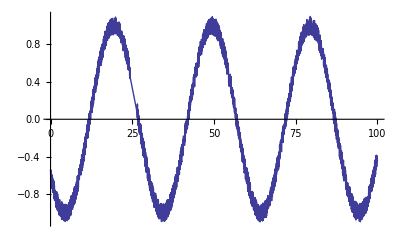

```mathematica
Plot[rotationFunction[1,30,10][2*10^6, 2*10^6,t],{t,0,100}]
```

```mathematica
Show[GraphicsArray[
Table[
ListDensityPlot[
Table[rotationFunction[3,60,10][x,y,fr],{x,0,1*10^7,3*10^5},{y,0,8.66025*10^6,3*10^5}],Mesh->False,AspectRatio->Automatic,Frame->None] ,{fr,0,20,1}]
],ImageSize->72*10]//Rasterize
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

## Rotation-- Da File Generation

```mathematica
rotationDa[rotationsPer2Pi_,framesPer2Pi_, noisePercent_]:=
Module[{tempdata},
tempdata=
Module[{coordinates},
Table[
coordinates=layout@getDetectorCoordinates[det];
Table[  rotationFunction[rotationsPer2Pi,framesPer2Pi,noisePercent][coordinates[[1]],coordinates[[2]],frame],
{frame, 0,1000}],
{det,0,471}]
];
SetDirectory[NotebookDirectory[]];
header[[5]]=Length[tempdata[[1]]];
data=BinaryWrite[ ".\\testfiles\\rotation_"<>ToString[rotationsPer2Pi]<>"_"<>ToString[framesPer2Pi]<>"_"<>ToString[noisePercent]<>".da",
Flatten[{header,Round[tempdata*1000/dataScale],footer}],
"Integer16"]
]
```

```mathematica
rotationDa[1,#, 10]& /@ Join[Range[5, 60, 2]]
```

{.\testfiles\rotation_1_5_10.da,.\testfiles\rotation_1_7_10.da,.\testfiles\rotation_1_9_10.da,.\testfiles\rotation_1_11_10.da,.\testfiles\rotation_1_13_10.da,.\testfiles\rotation_1_15_10.da,.\testfiles\rotation_1_17_10.da,.\testfiles\rotation_1_19_10.da,.\testfiles\rotation_1_21_10.da,.\testfiles\rotation_1_23_10.da,.\testfiles\rotation_1_25_10.da,.\testfiles\rotation_1_27_10.da,.\testfiles\rotation_1_29_10.da,.\testfiles\rotation_1_31_10.da,.\testfiles\rotation_1_33_10.da,.\testfiles\rotation_1_35_10.da,.\testfiles\rotation_1_37_10.da,.\testfiles\rotation_1_39_10.da,.\testfiles\rotation_1_41_10.da,.\testfiles\rotation_1_43_10.da,.\testfiles\rotation_1_45_10.da,.\testfiles\rotation_1_47_10.da,.\testfiles\rotation_1_49_10.da,.\testfiles\rotation_1_51_10.da,.\testfiles\rotation_1_53_10.da,.\testfiles\rotation_1_55_10.da,.\testfiles\rotation_1_57_10.da,.\testfiles\rotation_1_59_10.da}

### Testing

```mathematica
tempdata=
Module[{coordinates},
Table[
coordinates=layout@getDetectorCoordinates[det];
Table[  rotationFunction[7,7*10,10][coordinates[[1]],coordinates[[2]],frame],
{frame, 0,400}],
{det,0,471}]
];
```

```mathematica
NNMFramePlot[First[Transpose[tempdata]]]//Rasterize
```

-Graphics-

```mathematica
cd=SetDirectory[NotebookDirectory[]]
```

Z:\My Documents\k.vsd\_documents\_figures\vsdMeth\flow field

```mathematica
$ByteOrdering
```

-1

```mathematica
header[[5]]=Length[tempdata[[1]]]; header[[5]]
```

401

```mathematica
data=BinaryWrite[ "rotation_7_70_10.da",
Flatten[{header,Round[tempdata*1000/dataScale],footer}],
"Integer16"]
```

rotation_7_70_10.da

### Test

```mathematica
dataobj=NNMDataNew[cd<>"//rotation_7_70_10.da"];
```

```mathematica
ListLinePlot[dataobj@readDataTraceAbsolute[#]& /@ Range[0,463, 70 ] ]//Rasterize
```

-Graphics-

```mathematica
ListLinePlot[
Arg[K`hilbert[#].{1,ⅈ}]&  /@(dataobj@readDataTraceAbsolute[#]& /@ Range[0,463, 70 ])
] //Rasterize
```

-Graphics-

## SourceSpiral

```mathematica
Show[GraphicsArray[
Table[DensityPlot[
sourceFunction[20,10,25][x,y,fr]+ spiralFunction[7,5/7,5][x,y,fr],{x,0,1*10^7},{y,0,8.66025*10^6},
PlotPoints->100, Mesh->False,AspectRatio->Automatic,Frame->None] ,{fr,0,5,1}]
],ImageSize->72*10]//Rasterize
```

-Graphics-